```mathematica
<<(NotebookDirectory[]<>"DetectPeriodTools.wl")
```

## Code 52

```mathematica
code52rule={52, {2, 1}, 2};
```

```mathematica
Row[ClickToCopy[ArrayPlot[RunCA[code52rule, #, 100], ImageSize->Tiny], #]&/@RandomInteger[2^50, 10]]
```

-Graphics-514853605314083-Graphics-707408973978298-Graphics-1072411564673116-Graphics-331312698335015-Graphics-415542321552543-Graphics-494142681169665-Graphics-619449186672717-Graphics-1010351139762488-Graphics-256185396770657-Graphics-462765407165225

#### Many infinite classes of periodic and expanding solutions:

```mathematica
ArrayPlot[RunCA[code52rule,#, 50], ImageSize->Tiny]&/@{{1,1,0,1,1,1,1,0,1,1},{1, 0, 1, 1, 1, 1, 0, 1},{1, 0, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1},{1, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1}, {1, 1, 1, 0, 0, 0, 1, 1, 1, 1, 1,1, 0, 0, 0, 1, 1, 1},{1, 1, 1, 0, 0, 0, 1, 1, 1, 1, 1,1,1,1,1,1,1,1,1,1,1, 0, 0, 0, 1, 1, 1}, {1, 0, 0, 1, 1, 1, 1,  0, 1, 1}, {1, 0, 0, 1, 1,1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1,  0, 1, 1}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### vs code20

Code 52 and 20 differ only by one bit, so they often behave similarly.

```mathematica
IntegerDigits[52, 2, 6]
IntegerDigits[20, 2, 6]
```

{1,1,0,1,0,0}

{0,1,0,1,0,0}

Because of this, some code 20 solutions are also code 52 solutions:

```mathematica
Grid[Join[{{"Code20", "Code52"}},{ArrayPlot[RunCA[code20rule, #, 50], ImageSize->Tiny], ArrayPlot[RunCA[code52rule, #, 50], ImageSize->Tiny]}&/@{189,635,151,14871103,222678959859,595703,610999,22503642597,11221488970893447375,2810468130557941198319,10469510870511,187,360759087837221,2197520782601119,142082121178470981231,15903,125231}]]
```

Code20 | Code52
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

#### SolutionSearch

```mathematica
res=Sort@DedupSame[Join@@ParallelTable[DetectPeriod[code52rule, RandomInteger[2^50]], 100]];
```

```mathematica
Row[AArrayPlot[code52rule, #, ImageSize->Small]&/@res[[;;UpTo[12], "Canonical"]], "  "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

mostly just solutions from code20 or elements from the infinite classes...

## Enumerating Totalistic Rules

```mathematica
Grid[Partition[ParallelTable[Labeled[AArrayPlot[{i, {2, 1}, 2}, RandomInteger[1, 100], ImageSize->Small], i], {i, 0, 63}], 4]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Codes of interest:

```mathematica
coi={5, 11, 13, 20, 23, 52, 53};
Table[Labeled[AArrayPlot[{i, {2, 1}, 2}, RandomInteger[1, 100], ImageSize->Small], i], {i, coi}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
resCoi=Table[DedupSame[Join@@ParallelTable[DetectPeriod[{code, {2, 1}, 2}, i], {i, 1, 1000, 2}]], {code, coi}];

Column[Table[Row[Join[{"Code "<>ToString[coi[[coiIdx]]]<>":"},
ClickToCopy[AArrayPlot[{coi[[coiIdx]], {2, 1}, 2},#, ImageSize->Tiny], {coi[[coiIdx]], #}]&/@ resCoi[[coiIdx, ;;UpTo[15], "Canonical"]]], "    "], {coiIdx, Length[coi]}]]
```

Code 5:-Graphics-{5,107}-Graphics-{5,219}-Graphics-{5,257}-Graphics-{5,273}-Graphics-{5,443}-Graphics-{5,571}-Graphics-{5,623}-Graphics-{5,891}-Graphics-{5,985}-Graphics-{5,1137}-Graphics-{5,1147}-Graphics-{5,2289}-Graphics-{5,4593}-Graphics-{5,4603}-Graphics-{5,9201}
        Code 11:-Graphics-{11,55}-Graphics-{11,59}-Graphics-{11,111}-Graphics-{11,123}-Graphics-{11,139}-Graphics-{11,149}-Graphics-{11,151}-Graphics-{11,155}-Graphics-{11,169}-Graphics-{11,171}-Graphics-{11,187}-Graphics-{11,189}-Graphics-{11,195}-Graphics-{11,199}-Graphics-{11,207}
        Code 13:-Graphics-{13,319}-Graphics-{13,3831}-Graphics-{13,7671}-Graphics-{13,15351}-Graphics-{13,30711}-Graphics-{13,61431}-Graphics-{13,122871}-Graphics-{13,245751}-Graphics-{13,491511}-Graphics-{13,3932151}-Graphics-{13,15728631}-Graphics-{13,125829111}
        Code 20:-Graphics-{20,151}-Graphics-{20,187}-Graphics-{20,189}-Graphics-{20,635}-Graphics-{20,15903}
        Code 23:-Graphics-{23,2553}-Graphics-{23,5113}-Graphics-{23,7919}-Graphics-{23,7967}-Graphics-{23,10191}-Graphics-{23,20431}-Graphics-{23,31183}-Graphics-{23,62415}-Graphics-{23,124879}-Graphics-{23,491471}-Graphics-{23,982991}-Graphics-{23,999375}-Graphics-{23,65970697666511}
        Code 52:-Graphics-{52,55}-Graphics-{52,59}-Graphics-{52,111}-Graphics-{52,123}-Graphics-{52,149}-Graphics-{52,151}-Graphics-{52,155}-Graphics-{52,169}-Graphics-{52,171}-Graphics-{52,187}-Graphics-{52,189}-Graphics-{52,195}-Graphics-{52,199}-Graphics-{52,207}-Graphics-{52,213}
        Code 53:-Graphics-{53,63}-Graphics-{53,1023}-Graphics-{53,2047}-Graphics-{53,4095}-Graphics-{53,4287}-Graphics-{53,6719}-Graphics-{53,8191}-Graphics-{53,8575}-Graphics-{53,16383}-Graphics-{53,32767}-Graphics-{53,34303}-Graphics-{53,53759}-Graphics-{53,65535}-Graphics-{53,107519}-Graphics-{53,131071}

## Code 5

```mathematica
code5rule={5, {2, 1}, 2};
```

Generally, my current DetectPeriod[] implementation might not work as expected for odd rules. In particular, the definition of  “persistent solution” that I used to implement it might be a little too over-inclusive, but it can be filtered out by hand.

Using a combination of automated and manual search, here are some unique solutions I found.
In some cases, these solutions are examples from an infinite family. In all such cases I include two examples from that family.

```mathematica
{257,273, 107,7340027, 18297,37748601,2915919,3058016714319, 4823785082879, 632263166436249599}
Row[AArrayPlot[code5rule,#, 100, Mesh->True]&/@%, "    "]
```

{257,273,107,7340027,18297,37748601,2915919,3058016714319,4823785082879,632263166436249599}

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## Code 23

```mathematica
code23rule={23, {2, 1}, 2};
```

```mathematica
AArrayPlot[code23rule,Echo@RandomInteger[2^500],200]
```

354677341044682991030356359699884473356929984502171591282763580271619355629564070422040507190863407345939171163864326873798382386011344277284293766426

-Graphics-

etc. some interesting structures

## Enumerating Totalistic Rules (r=3)

```mathematica
Grid[Partition[ParallelTable[Labeled[AArrayPlot[{i, {2, 1}, 3}, RandomInteger[1, 100], ImageSize->Small], i], {i, 0, 255}], 4]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

### Code 168

```mathematica
AArrayPlot[{168, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res168=DedupSame[Join@@ParallelTable[DetectPeriod[{168, {2, 1}, 3}, RandomInteger[2^100]], 1000000]];
```

```mathematica
Row[Labeled[AArrayPlot[{168, {2, 1}, 3}, #], #]&/@res168[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Code 164

```mathematica
AArrayPlot[{164, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res164=DedupSame[Join@@ParallelTable[DetectPeriod[{164, {2, 1}, 3}, RandomInteger[2^100]], 200000]];
```

```mathematica
Row[Labeled[AArrayPlot[{164, {2, 1}, 3}, #], #]&/@res164[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics-

### Code 100

```mathematica
AArrayPlot[{100, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res100=DedupSame[Join@@ParallelTable[DetectPeriod[{100, {2, 1}, 3}, RandomInteger[2^100]], 200000]];
```

```mathematica
Row[Labeled[AArrayPlot[{100, {2, 1}, 3}, #], #]&/@res100[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### Code 40

```mathematica
AArrayPlot[{40, {2, 1}, 3},RandomInteger[2^200]]
```

-Graphics-

```mathematica
res40=DedupSame[Join@@ParallelTable[DetectPeriod[{40, {2, 1}, 3}, RandomInteger[2^100]], 200000]];
```

```mathematica
Row[Labeled[AArrayPlot[{40, {2, 1}, 3}, #], #]&/@res40[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### Code 36

```mathematica
AArrayPlot[{36, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res36=DedupSame[Join@@ParallelTable[DetectPeriod[{36, {2, 1}, 3}, RandomInteger[2^100]], 200000]];
```

```mathematica
Row[Labeled[AArrayPlot[{36, {2, 1}, 3}, #], #]&/@res36[[All, "Canonical"]], "   "]
```

-Graphics-

### Code 180

```mathematica
AArrayPlot[{180, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res180=DedupSame[Join@@ParallelTable[DetectPeriod[{180, {2, 1}, 3}, i], {i, 1, 10, 2}]];
```

```mathematica
Row[Labeled[AArrayPlot[{180, {2, 1}, 3}, #], #]&/@res180[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics-

### Code 152

```mathematica
AArrayPlot[{152, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res152=DedupSame[Join@@ParallelTable[DetectPeriod[{152, {2, 1}, 3}, RandomInteger[2^100]], 100000]];
```

```mathematica
Row[Labeled[AArrayPlot[{152, {2, 1}, 3}, #], #]&/@res152[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
res152other=DedupSame[Join@@ParallelTable[DetectPeriod[{152, {2, 1}, 3},i], {i, 1, 1000000, 2}]];
```

```mathematica
Row[Labeled[AArrayPlot[{152, {2, 1}, 3}, #], #]&/@res152other[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics-

### Code 88

```mathematica
AArrayPlot[{88, {2, 1}, 3}, RandomInteger[2^200]]
```

-Graphics-

```mathematica
res88=DedupSame[Join@@ParallelTable[DetectPeriod[{88, {2, 1}, 3},i], {i, 1, 10000, 2}]];
```

```mathematica
Row[Labeled[AArrayPlot[{88, {2, 1}, 3}, #], #]&/@res88[[All, "Canonical"]], "   "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
VisualizeDetectPeriod[{88, {2, 1}, 3},5063]
```

-Graphics--Graphics--Graphics-

What an incredible glider gun!

```mathematica
AArrayPlot[{88, {2, 1}, 3},5063, 500]
```

-Graphics-

## Enumerating Totalistic Rules (k=3, r=1)

```mathematica
(* Grid[Partition[ParallelTable[Labeled[AArrayPlot[{i, {3, 1}, 1}, RandomInteger[2, 100], ImageSize->Small], i], {i, 0, 3^7-1, 3}], 4]] *)
```

Codes of interest:

```mathematica
coi={114,141,195, 198, 306, 357, 384, 438, 600, 627, 705, 843, 924, 1086, 1278, 1329, 1350, 1572, 1764};
```

```mathematica
ParallelTable[Labeled[AArrayPlot[{i, {3, 1}, 1}, RandomInteger[2, 100], ImageSize->Small], i], {i, coi}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Inspecting Particular

```mathematica
InspectCode[code_]:=Quiet[
PrintTemporary["Inspecting ", code];
res[code]=DedupSame[Join@@ParallelTable[TimeConstrained[DetectPeriod[{code, {3, 1}, 1}, RandomInteger[3^100]], 2, {}], 10000]];

{"Code "<>ToString[code]<>":",AArrayPlot[{code, {3, 1}, 1}, RandomInteger[3^100]],Row[Labeled[AArrayPlot[{code, {3, 1}, 1}, #], ClickToCopy[#, {code, #}]]&/@res[code][[All, "Original"]], "   "]}
]
```

```mathematica
InspectCode[1329]
```

{Code 1329:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

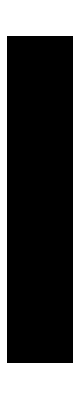
{Code 114:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 141:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 357:,-Graphics-,      -Graphics--Graphics--Graphics-}
{Code 600:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 843:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 1086:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 1278:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 1329:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}
{Code 1572:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
Column[InspectCode/@{114, 141, 357, 600, 843, 1086, 1278, 1329, 1572}]
```

## New

```mathematica
Grid[Partition[ParallelTable[Labeled[AArrayPlot[{i, {3, 1}, 2}, RandomInteger[2, 100],ImageSize->Small], i], {i, RandomSample[Range[0, 177146, 3], 100]}], 4]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
InspectCode[24633]
```

{Code 24633:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
InspectCode[code_, num_:1000]:=Quiet[
PrintTemporary["Inspecting ", code];
res[code]=DedupSame[Join@@ParallelTable[TimeConstrained[DetectPeriod[{code, {3, 1}, 2}, RandomInteger[3^100]], 2, {}], num]];

{"Code "<>ToString[code]<>":",AArrayPlot[{code, {3, 1}, 2}, RandomInteger[3^100]],Row[Labeled[AArrayPlot[{code, {3, 1}, 2}, #], ClickToCopy[#, {code, #}]]&/@res[code][[All, "Canonical"]], "   "]}
]
```

```mathematica
InspectCode[74145, 100]
```

{Code 74145:,-Graphics-,      -Graphics-}

```mathematica
AArrayPlot[{24633, {3, 1}, 2}, Echo@RandomInteger[3^300], 300]
```

77338067979923253929334964987379502610361876726536211896159401189220619737654137747954555115205914018783454006702275514555725272119112556636355

-Graphics-

```mathematica
InspectCode[74145, 100]
```

{Code 74145:,-Graphics-,      -Graphics--Graphics--Graphics-}

```mathematica
AArrayPlot[{74145, {3, 1}, 2}, Echo@RandomInteger[3^100], 300]
```

426385363283616132609154653845436081048832700951

-Graphics-

```mathematica
AArrayPlot[{74145, {3, 1}, 2}, Echo@RandomInteger[3^100], 300]
```

426385363283616132609154653845436081048832700951

-Graphics-

```mathematica
AArrayPlot[{120075, {3, 1}, 2}, {1, 2, 2, 2}]
```

-Graphics-

```mathematica
AArrayPlot[{159120, {3, 1}, 2}, 77809102926733709016215739901224806584620658087598898460116492007790066224798225505162260254785701655270288420816634391937892544493895608235147364999736833592865900740680545711581687521194772, 400]
```

-Graphics-

```mathematica
InspectCode[159120]
```

{Code 159120:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
InspectCode[54222]
```

{Code 54222:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
InspectCode[110841]
```

{Code 110841:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
init=RandomInteger[2,100];
```

```mathematica
AArrayPlot[{5616, {3, 1}, 2}, {1, 2, 2, 2, 1, 1, 2, 2, 1}, 1000]
```

-Graphics-

```mathematica
AArrayPlot[{153684, {3, 1}, 2},Echo@RandomInteger[3^300], 100]
```

104564571529590141309990292552339583411383926371976969412967279819133678217972515421244147446258109395450469636410326574051721016390443234236069

-Graphics-

```mathematica
InspectCode[153684,100000]
```

{Code 153684:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
AArrayPlot[{61911, {3, 1}, 2},155, 300]
```

-Graphics-

```mathematica
AArrayPlot[{58572, {3, 1}, 2},11095511979354300294000446448086370876744302007, 1000]
```

-Graphics-

```mathematica
InspectCode[58572, 100]
```

{Code 58572:,-Graphics-,      -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
AArrayPlot[{32619, {3, 1}, 2},Echo@RandomInteger[3^300], 1000]
```

22735944270666591058081384555352194635592900449343272523035541357144665784581388764120429914267432583740826892572023133808191629462172689311052

-Graphics-

```mathematica
AArrayPlot[{74145, {3, 1}, 2},17,3000]
```

-Graphics-

```mathematica
RunCA[{74145, {3, 1}, 2},17,{{{3000}}}]
```

```mathematica
AArrayPlot[{74145, {3, 1}, 2},[[;;1300]],1000]
```

-Graphics-

```mathematica
FromDigits[StripZeros[[[;;1300]]], 3]
```

9082813861276790440779001835238459918634469173657957778628512824139488972208025068779083144126996167705260775548119320648150559465179381640610327409780156104750587999127144286511844502711214900107050376435048297464321579899677064466919476482424409260733863803006835059415364983451943482554396114098319507154771980916565454812259643875189197930390830953455489426524523571702920579509047155672682972407008560013678941195563572622705292899788967808745855116814687760488937544450387471390941341881631728831077305771396607642052055111055080005960515104347894467002875789999435845782810328341501912186310814454222

```mathematica
AArrayPlot[{74145, {3, 1}, 2},9082813861276790440779001835238459918634469173657957778628512824139488972208025068779083144126996167705260775548119320648150559465179381640610327409780156104750587999127144286511844502711214900107050376435048297464321579899677064466919476482424409260733863803006835059415364983451943482554396114098319507154771980916565454812259643875189197930390830953455489426524523571702920579509047155672682972407008560013678941195563572622705292899788967808745855116814687760488937544450387471390941341881631728831077305771396607642052055111055080005960515104347894467002875789999435845782810328341501912186310814454222,3000]
```

-Graphics-

```mathematica
AArrayPlot[{120075, {3, 1}, 2}, {2, 1, 2}]
```

-Graphics-

```mathematica
IntegerDigits[9082813861276790440779001835238459918634469173657957778628512824139488972208025068779083144126996167705260775548119320648150559465179381640610327409780156104750587999127144286511844502711214900107050376435048297464321579899677064466919476482424409260733863803006835059415364983451943482554396114098319507154771980916565454812259643875189197930390830953455489426524523571702920579509047155672682972407008560013678941195563572622705292899788967808745855116814687760488937544450387471390941341881631728831077305771396607642052055111055080005960515104347894467002875789999435845782810328341501912186310814454222, 3]
```

```mathematica
AArrayPlot[{74145, {3, 1}, 2},Join[{1,0,1,0,2,2,2,2,2,2,0,2,2,0,0,0,0,1,1,1,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,1,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,2,0,2,2,2,2,0,2,0,0,0,0,1,0,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,2,0,2,0,2,2,2,2,2,2,1,2,0,2,1,0,1,1,0,0,1,1,1,1,2,2,2,0,2,2,0,2,2,2,1,0,1,0,0,1,0,1,1,0,0,1,0,2,2,0,2,1,1,0,1,0,0,1,1,1,1,1,0,1,0,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,1,1,1,1,0,2,2,1,1,0,2,0,2,1,0,1,0,0,0,2,2,2,2,1,1,2,0,2,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,2,2,2,2,2,2,0,2,2,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,1,1,1,1,0,0,2,0,0,1,0,1,2,0,2,2,2,0,2,2,2,2,0,2,0,2,2,2,2,2,0,2,0,1,0,2,0,2,2,2,2,2,2,0,2,2,2,2,2,1,1,2,0,2,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,2,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,1,2,0,2,0,0,0,1,1,0,2,2,0,2,2,0,2,2,2,2,1,2,0,2,0,0,1,1,0,2,2,2,2,2,0,2,0,0,0,1,0,1,1,0,1,0,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,0,2,2,1,2,0,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,2,2,0,0,0,0,0,0,0,0,1,0,1,0,2,0,2,2,2,2,2,2,0,2,2,2,2,2,2,2,0,2,0,2,2,2,0,2,0,2,2,2,2,2,2,2,2,0,0,2,0,1,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,1,1,0,0,0,2,2,2,0,2,2,1,2,2,2,2,2,2,2,2,0,1,1,1,1,1,1,0,0,1,0,0,0,0,0,1,1,1,0,0,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,2,0,2,1,1,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,2,2,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,2,1,0,0,0,2,0,2,2,2,2,2,2,2,2,2,2,2,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,1,0,2,2,2,1,1,1,1,2,2,2,2,2,2,0,2,2,2,0,2,0,2,0,0,0,1,1},ConstantArray[0, 6],{1,1,0,0,0,2,0,2,0,2,2,2,0,2,2,2,2,2,2,1,1,1,1,2,2,2,0,1,1,1,0,0,1,1,1,0,0,0,0,0,1,1,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,2,2,2,2,2,2,2,2,2,2,2,0,2,0,0,0,1,2,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,1,1,2,0,2,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,2,0,0,1,1,1,0,0,0,0,0,1,0,0,1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,1,2,2,0,2,2,2,0,0,0,1,1,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,1,0,2,0,0,2,2,2,2,2,2,2,2,0,2,0,2,2,2,0,2,0,2,2,2,2,2,2,2,0,2,2,2,2,2,2,0,2,0,1,0,1,0,0,0,0,0,0,0,0,2,2,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,0,2,1,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,1,1,0,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,0,1,0,1,1,0,1,0,0,0,2,0,2,2,2,2,2,0,1,1,0,0,2,0,2,1,2,2,2,2,0,2,2,0,2,2,0,1,1,0,0,0,2,0,2,1,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,2,0,2,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,2,0,2,1,1,2,2,2,2,2,0,2,2,2,2,2,2,0,2,0,1,0,2,0,2,2,2,2,2,0,2,0,2,2,2,2,0,2,2,2,0,2,1,0,1,0,0,2,0,0,1,1,1,1,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,2,2,0,2,2,2,2,2,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,2,0,2,1,1,2,2,2,2,0,0,0,1,0,1,2,0,2,0,1,1,2,2,0,1,1,1,1,2,2,2,2,2,0,1,1,1,2,2,2,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,0,1,0,1,1,1,1,1,0,0,1,0,1,1,2,0,2,2,0,1,0,0,1,1,0,1,0,0,1,0,1,2,2,2,0,2,2,0,2,2,2,1,1,1,1,0,0,1,1,0,1,2,0,2,1,2,2,2,2,2,2,0,2,0,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,0,1,0,0,0,0,2,0,2,2,2,2,0,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,1,0,1,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,1,1,1,0,0,0,0,2,2,0,2,2,2,2,2,2,0,1,0,1}], 1000, ImageSize->{Automatic, 100}]
```

-Graphics-

```mathematica
AArrayPlot[{74145, {3, 1}, 2},,300]
```

-Graphics-

```mathematica
Reverse@IntegerDigits[9082813861276790440779001835238459918634469173657957778628512824139488972208025068779083144126996167705260775548119320648150559465179381640610327409780156104750587999127144286511844502711214900107050376435048297464321579899677064466919476482424409260733863803006835059415364983451943482554396114098319507154771980916565454812259643875189197930390830953455489426524523571702920579509047155672682972407008560013678941195563572622705292899788967808745855116814687760488937544450387471390941341881631728831077305771396607642052055111055080005960515104347894467002875789999435845782810328341501912186310814454222, 3]
```

{2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,2,0,2,0,2,2,2,0,2,2,2,2,2,2,1,1,1,1,2,2,2,0,1,1,1,0,0,1,1,1,0,0,0,0,0,1,1,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,2,2,2,2,2,2,2,2,2,2,2,0,2,0,0,0,1,2,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,1,1,2,0,2,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,2,0,0,1,1,1,0,0,0,0,0,1,0,0,1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,1,2,2,0,2,2,2,0,0,0,1,1,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,1,0,2,0,0,2,2,2,2,2,2,2,2,0,2,0,2,2,2,0,2,0,2,2,2,2,2,2,2,0,2,2,2,2,2,2,0,2,0,1,0,1,0,0,0,0,0,0,0,0,2,2,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,0,2,1,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,1,1,0,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,0,1,0,1,1,0,1,0,0,0,2,0,2,2,2,2,2,0,1,1,0,0,2,0,2,1,2,2,2,2,0,2,2,0,2,2,0,1,1,0,0,0,2,0,2,1,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,2,0,2,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,2,0,2,1,1,2,2,2,2,2,0,2,2,2,2,2,2,0,2,0,1,0,2,0,2,2,2,2,2,0,2,0,2,2,2,2,0,2,2,2,0,2,1,0,1,0,0,2,0,0,1,1,1,1,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,2,2,0,2,2,2,2,2,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,2,0,2,1,1,2,2,2,2,0,0,0,1,0,1,2,0,2,0,1,1,2,2,0,1,1,1,1,2,2,2,2,2,0,1,1,1,2,2,2,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,2,2,2,2,0,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,0,1,0,1,1,1,1,1,0,0,1,0,1,1,2,0,2,2,0,1,0,0,1,1,0,1,0,0,1,0,1,2,2,2,0,2,2,0,2,2,2,1,1,1,1,0,0,1,1,0,1,2,0,2,1,2,2,2,2,2,2,0,2,0,2,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,0,1,0,0,0,0,2,0,2,2,2,2,0,2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,1,0,1,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,1,1,1,0,0,0,0,2,2,0,2,2,2,2,2,2,0,1,0,1}